```mathematica
(* This notebook contains examples for the PET-functions;
-CalcRea-               calculate equilibrium data of reactions;
 -Dgr-                   calculate delta-G(R) of a reaction;
 -PlotRea-               plot calculated reactions;
 -CalcReaIntersection-   calculate the intersection of reactions;
-MakeCompositionMatrix-  calculate the composition matrix of a list of phase components; 
 -MakeRea-               calculate reaction stoichiometries;
-SelectRea-              select specific reactions from a total list of reactions;
*)
(* This top-cell must be run once before any example can be performed.  *)

(* Define the directory,where the PET-files reside (e.g. C:\Eigene Dateien\Pet) and load PET. *)$PetDirectory="C:\Dokumente und Einstellungen\dachsedgar\Eigene Dateien\Pet\Pet7.0";

SetDirectory[$PetDirectory];
DeclarePackage["DEFDAT`",{"Dataset"}];
Dataset[Dataset-> B88];
```

```mathematica
(* display the usage for the PET-functions -CalcRea-  *) 
CalcRea::usage
```

CalcRea[rea] calculates equilibrium data of reactions.
<rea> is produced with -MakeRea- (see examples in PET_CalcRea.nb and MakeRea::usage).
The following options are available with -CalcRea-:

Name           value                 meaning

CalcReaMode -> PT (default)          P-T diagram (find equilibrium-T's of a reaction for given P's)
               TP                    P-T diagram (find equilibrium-P's of a reaction for given T's (in C))
               TXCO2                 T-X(CO2) diagram (find equilibrium-T's of a reaction for given X(CO2)'s and P)
               TXH2                  T-X(H2) diagram (find equilibrium-T's of a reaction for given X(H2)'s and P)
               TXH2logfO2            as TXH2, but convert calculated T-X(H2) data to corresponding logf(O2)-T data
               logfO2T               logf(O2)-T diagram (find equilibrium-logf(O2)'s of a reaction for given T's and P)
CalcReaMin ->  1000 (default)        Minimum value at which calculation starts:
                                                   in PT-mode: P(min) in bars
                                                   in TP-mode: T(min) in Celsius
                                                   in TXCO2-mode: X(CO2)min
                                                   in TXH2-mode: X(H2)min
                                                   in TXH2logfO2-mode: X(H2)min
                                                   in logfO2T-mode: T(min) in Celsius
CalcReaMax ->  10000 (default)       Maximum value in calculation: in PT-mode: P(max) in bars
                                                   in TP-mode: T(max) in Celsius
                                                   in TXCO2-mode: X(CO2)max
                                                   in TXH2-mode: X(H2)max
                                                   in TXH2logfO2-mode: X(H2)max
                                                   in logfO2T-mode: T(max) in Celsius
Steps ->       10 (default)          number of steps between minimum and maximum value (including both) in the calculation
Screen ->      ScreenYes (default)   print equilibrium data to the screen during calculation
               ScreenNo              don't print equilibrium data to the screen during calculation
SampleFile -> "None" (default)       define a sample file to be used in the calculation
OutputFile -> "None" (default)       define an output file to which calculated data are written

If a sample file is specified, -CalcRea- uses the PET-function -Activity- to calculate activities
of phase components for that sample (see Activity::usage for more details).
For equilibria with flat slopes, -CalcRea- in PT-mode may not find a solution in the range Pmin < P < Pmax.
Use the option CalcReaMode -> TP in this case.
Data are saved to the file "OutputFile.ptx", if an output-file is specified.
Data may be plotted with -PlotRea- and intersections of reactions may be calculated with -CalcReaIntersection-.
ReturnValue:
{{{{reaction stoichiometry},{activities used},{list of P-T data}}},{info on dataset and sample file}}
Example:
phases = {mu, qz, san, ky, h2o};
rea = MakeRea[phases]
result = CalcRea[rea]
ReturnValue:
{{{{-1 mu, -1 qz, 1 h2o, 1 ky, 1 san},{a(mu)=1, a(qz)=1, a(h2o)=1, a(ky)=1, a(san)=1},
{{601.111,1000.},{642.39,2000.},{673.724,3000.},{701.018,4000.},{725.864,5000.},
{748.972,6000.},{770.734,7000.},{791.396,8000.},{811.126,9000.},{830.045,10000.}}}},
{Dataset -> B,SampleFile->None}}
For further examples see PET_CalcRea.nb.
Called from: User.
Calls: -Dgr-, -Activity-, -SaveRea-.
Package name: DG.m
PET: Petrological Elementary Tools, (c) Edgar Dachs.

```mathematica
(*  ---------------------------------------    -CalcRea-    -----------------------------------------  *)
(*  ---------------------------------------  P-T equilibria  -----------------------------------------  *)
(* Example 1: Use the PET function -CalcRea- to calculate the equilibrium 
Mu + Qz = San + Ky + H2O for pure phase components;
Change the default settings of the options CalcReaMin, CalcReaMax and Step in -CalcRea- and save data to the file "test"  *)
 
phases={mu,qz,san,ky,h2o}; (* define phase components in the list "phases"  *)
rea=MakeRea[phases] ;                       (* calculate the reaction stoichiometry relating the phase components *)
result=CalcRea[rea,CalcReaMin->1000,CalcReaMax->3000,Steps->3,OutputFile->"test"]
```

calculating PT data of the reaction:

{-1. mu,-1. qz,1. h2o,1. ky,1. san}

1000 601.111

2000. 642.39

3000. 673.724

Equilibrium data have been stored in the file test.ptx.

{{{{-1. mu,-1. qz,1. h2o,1. ky,1. san},{a(mu)=1, a(qz)=1, a(h2o)=1, a(ky)=1, a(san)=1},{{601.111,1000.},{642.39,2000.},{673.724,3000.}}}},{Dataset -> B88,SampleFile->None}}

```mathematica
(* Example 2: Use the PET function -CalcRea- to calculate the equilibrium 
Mu + Qz = San + Ky + H2O for X(H2O) = 0.9 assuming a H2O-CO2 fluid *) 

phases={mu,qz,san,ky,h2o}; (* define phase components in the list "phases"  *)
rea=MakeRea[phases] ;                       (* calculate the reaction stoichiometry relating the phase components *)
rea={{rea[[1]],{1,1,0.9,1,1}}};  (* append the activity list {1,1,0.9,1,1} to rea *)
result=CalcRea[rea]
```

calculating PT data of the reaction:

{{-1. mu,-1. qz,1. h2o,1. ky,1. san},{1,1,0.9,1,1}}

1000 591.058

2000. 631.017

3000. 661.363

{{{{{-1. mu,-1. qz,1. h2o,1. ky,1. san},{1,1,0.9,1,1}},{a(mu)=1, a(qz)=1, a(h2o)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(ky)=1, a(san)=1},{{591.058,1000.},{631.017,2000.},{661.363,3000.}}}},{Dataset -> B88,SampleFile->None}}

```mathematica
(* Example 3: Use the PET function -CalcRea- to calculate the equilibrium 
Mu + Qz = San + Ky + H2O 
using data for white mica from sample file "hs78b" to calculate the activity of the ms phase-component  *) 

phases={mu,qz,san,ky,h2o}; (* define phase components in the list "phases"  *)
rea=MakeRea[phases]                      (* calculate the reaction stoichiometry relating the phase components *)
result=CalcRea[rea,SampleFile->"hs78b",OutputFile->"test"]
```

{{-1. mu,-1. qz,1. h2o,1. ky,1. san}}

calculating PT data of the reaction:

{-1. mu,-1. qz,1. h2o,1. ky,1. san}

1000 635.968

2000. 683.631

3000. 718.717

Equilibrium data have been stored in the file test.ptx.

{{{{-1. mu,-1. qz,1. h2o,1. ky,1. san},{a(mu)=WmChatterjeeFroese, a(qz)=1, a(h2o)=1, a(ky)=1, a(san)=1},{{635.968,1000.},{683.631,2000.},{718.717,3000.}}}},{Dataset -> B88,SampleFile->hs78b}}

```mathematica
(* Example 4: Use the PET function -CalcRea- to calculate the equilibrium 
Mu + Qz = San + Ky + H2O 
for white mica composition from sample file "hs78b";
Use ideal-activities of the ms phase-component.  *) 

phases={mu,qz,san,ky,h2o}; (* define phase components in the list "phases"  *)
rea=MakeRea[phases];                        (* calculate the reaction stoichiometry relating the phase components *)
SetOptions[ActivityHP,ActivityMode->IdealActivity]; SetOptions[ActivityB,ActivityMode->IdealActivity]; (* -ACTIVITB- is the PET function for activities in combination with Berman data set *)
result=CalcRea[rea,SampleFile->"hs78b"]
```

calculating PT data of the reaction:

{-1. mu,-1. qz,1. h2o,1. ky,1. san}

1000 645.273

2000. 695.745

3000. 733.272

{{{{-1. mu,-1. qz,1. h2o,1. ky,1. san},{a(mu)=Ideal, a(qz)=1, a(h2o)=1, a(ky)=1, a(san)=1},{{645.273,1000.},{695.745,2000.},{733.272,3000.}}}},{Dataset -> B88,SampleFile->hs78b}}

```mathematica
(* Example 5a: Use the PET function -CalcRea- to calculate the Al2SiO5 phase diagram (only stable parts). *) 
phases={ky,sil,and}; (* define phase components in the list "phases"  *)
(* calculate the reaction stoichiometry relating the phase components: use option MakeReaMode->1 to find all reactions *)

rea=MakeRea[phases,MakeReaMode->1] 
result=CalcRea[rea,CalcReaMode->PT,CalcReaMin->1000,CalcReaMax->10000,Steps->10,Screen->ScreenNo]
```

Calculating reactions with 2 phases

(degree of freedom =  1 ): from combinatorics, there are 3 possible reactions.

{{-1. ky,1. and},{-1. sil,1. and},{-1. ky,1. sil}}

calculating PT data of the reaction:

{-1. ky,1. and}

calculating PT data of the reaction:

{-1. sil,1. and}

calculating PT data of the reaction:

{-1. ky,1. sil}

{{{{-1. ky,1. and},{a(ky)=1, a(sil)=1},{{279.168,1000.},{361.374,2000.},{444.225,3000.},{528.075,4000.},{613.347,5000.},{700.509,6000.},{790.078,7000.},{882.635,8000.},{978.848,9000.},{1079.52,10000.}}},{{-1. sil,1. and},{a(ky)=1, a(sil)=1},{{684.579,1000.},{614.832,2000.},{550.006,3000.},{489.964,4000.},{434.433,5000.},{383.049,6000.},{335.41,7000.},{291.102,8000.},{249.721,9000.},{210.883,10000.}}},{{-1. ky,1. sil},{a(ky)=1, a(sil)=1},{{381.636,1000.},{426.733,2000.},{472.119,3000.},{517.775,4000.},{563.684,5000.},{609.827,6000.},{656.188,7000.},{702.75,8000.},{749.497,9000.},{796.415,10000.}}}},{Dataset -> B88,SampleFile->None}}

{{3732.81,505.55,{1,2}},{3732.82,505.551,{1,3}},{3732.81,505.55,{2,3}}}

calculating PT data of the reaction:

{-1. ky,1. and}

calculating PT data of the reaction:

{-1. sil,1. and}

calculating PT data of the reaction:

{-1. ky,1. sil}

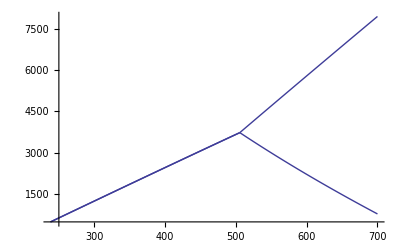

```mathematica
(* Example 5a continued: use the PET-function -CalcReaIntersection-to calculate the intersections 
and then recalculate each reaction and plot the result. *)

i = CalcReaIntersection[result]
r1= CalcRea[{rea[[1]]},CalcReaMode->PT,CalcReaMin->500,CalcReaMax->i[[1,1]],Steps->20,Screen->ScreenNo,OutputFile->"None"];
r2= CalcRea[{rea[[2]]},CalcReaMode->TP,CalcReaMin->i[[1,2]],CalcReaMax->700,Steps->20,Screen->ScreenNo,OutputFile->"None"];
r3= CalcRea[{rea[[3]]},CalcReaMode->TP,CalcReaMin->i[[1,2]],CalcReaMax->700,Steps->20,Screen->ScreenNo,OutputFile->"None"];
PlotRea[Join[r1[[1]],r2[[1]],r3[[1]]]]
```

Calculating reactions with 2 phases

(degree of freedom =  1 ): from combinatorics, there are 3 possible reactions.

calculating PT data of the reaction:

{-1. ky,1. and}

calculating PT data of the reaction:

{-1. sil,1. and}

calculating PT data of the reaction:

{-1. ky,1. sil}

calculating PT data of the reaction:

{-1. ky,1. and}

calculating PT data of the reaction:

{-1. sil,1. and}

calculating PT data of the reaction:

{-1. ky,1. sil}

calculating PT data of the reaction:

{-1. ky,1. and}

calculating PT data of the reaction:

{-1. sil,1. and}

calculating PT data of the reaction:

{-1. ky,1. sil}

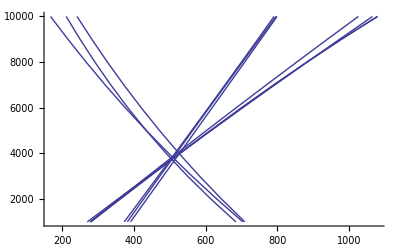

```mathematica
(* Example 5b: Use the PET function -CalcRea- to calculate the Al2SiO5 phase diagram: Compare the three data sets *) 
phases={ky,sil,and}; (* define phase components in the list "phases"  *)
(* calculate the reaction stoichiometry relating the phase components: use option MakeReaMode->1 to find all reactions *)

rea=MakeRea[phases,MakeReaMode->1] ;
Dataset[Dataset->B88];
result1=CalcRea[rea,CalcReaMode->PT,CalcReaMin->1000,CalcReaMax->10000,Steps->10,Screen->ScreenNo];
Dataset[Dataset->HP32];  
result2=CalcRea[rea,CalcReaMode->PT,CalcReaMin->1000,CalcReaMax->10000,Steps->10,Screen->ScreenNo];
Dataset[Dataset->G97];  
result3=CalcRea[rea,CalcReaMode->PT,CalcReaMin->1000,CalcReaMax->10000,Steps->10,Screen->ScreenNo];

PlotRea[Join[result1[[1]],result2[[1]],result3[[1]]]]
```

Message from -CalcFormula- (PET -> TWEEQ interface): creating file "hs78b.oxi".

Use Cmp.exe to create a *.cmp file for further calculations with PET or TWEEQ.

Message from -CalcFormula-: creating file "hs78b.fu".

calculating PT data of the reaction:

{-3. an,1. gr,2. ky,1. qz}

1000 328.543

2000. 379.693

3000. 430.72

4000. 481.588

5000. 532.26

6000. 582.7

7000. 632.876

8000. 682.758

9000. 732.322

10000. 781.547

calculating PT data of the reaction:

{-1. alm,-1. phl,1. ann,1. py}

1000 464.944

2000. 469.823

3000. 474.684

4000. 479.528

5000. 484.353

6000. 489.16

7000. 493.95

8000. 498.721

9000. 503.475

10000. 508.21

{{{{-3. an,1. gr,2. ky,1. qz},{a(alm)=GrtBerman, a(phl)=BtMcMullin, a(ann)=BtMcMullin, a(py)=GrtBerman},{{328.543,1000.},{379.693,2000.},{430.72,3000.},{481.588,4000.},{532.26,5000.},{582.7,6000.},{632.876,7000.},{682.758,8000.},{732.322,9000.},{781.547,10000.}}},{{-1. alm,-1. phl,1. ann,1. py},{a(alm)=GrtBerman, a(phl)=BtMcMullin, a(ann)=BtMcMullin, a(py)=GrtBerman},{{464.944,1000.},{469.823,2000.},{474.684,3000.},{479.528,4000.},{484.353,5000.},{489.16,6000.},{493.95,7000.},{498.721,8000.},{503.475,9000.},{508.21,10000.}}}},{Dataset -> B88,SampleFile->hs78b}}

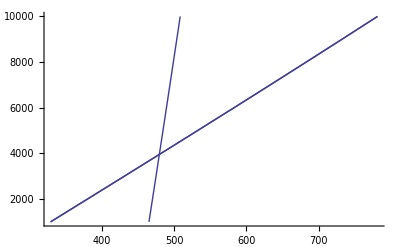

{{3955.16,479.311,{1,2}}}

```mathematica
(* 
Example 6: Use the PET function -CalcRea- to calculate the grt-bt and GASP equilibrium for sample "hs78b"; 
Use -PlotRea- to plot the reactions and -CalcReaIntersection- to calculate their intersection; First apply

CalcFormula["hs78b"];

to calculate the mineral formulae for "hs78b" (this also creates the file "hs78b.oxi); 
Then in Windows Explorer run CMP.EXE and use hs78b.oxi as data file (this creates the TWEEQ-file "hs78b.cmp");
For unknown reasons CMP.EXE does not produce mole fractions for the plag in "hs78b", but writes **** for PLAG:

BIOT [xMg-][xFe-][-xTi][-xAl][-xK-][-xOH]
BIOT .3922 .4022 .0282 .1747 0.76181.0000
MICA [-xK-][-xNa][xAl-][-xOH]
MICA .7539 .2461 .9457 1.0000
GARN [-Gr-][-Py-][-Alm][-Sp-]
GARN .0254 .0934 .7691 .1121
PLAG [-An-][-Ab-][-Or-]
PLAG ************.0000

As can be seen from the file "hs78b.fu" (formula units created by -CalcFormula-): X(An) = 0.1173, X(Ab) = 0.8769.
Correct these data manually in the file "hs78b.cmp" as shown below:
PLAG [-An-][-Ab-][-Or-]
PLAG .1173 .8769 .0000

-CalcRea- reads these data for activity calculations; 
The use of CMP.EXE helps maintaining consistency between cation recalculation and thermodynamic data set;
*)

Dataset[Dataset->B88];
CalcFormula["hs78b"];
phases={ann,phl,alm,py,gr,an,ky,qz};
rea=MakeRea[phases];
SetOptions[ActivityB,ActivityMode->RealActivity];SetOptions[ActivityHP,ActivityMode->RealActivity];
result=CalcRea[rea,CalcReaMin->1000,CalcReaMax->10000,Steps->10,CalcReaMode->PT,SampleFile->"hs78b"]
PlotRea[result]
CalcReaIntersection[result]
```

```mathematica
(* Example 7: Use the PET function -Dgr- to calculate delta-G(R) of the reaction:
3 An = Gr + 2 Ky + Qz for P = 10 kbar, T = 800 K.   *)

phases = {gr,an,ky,qz}; 
rea =MakeRea[phases];          
Dgr[rea[[1]],10000,800,"None"]
```

{1906.65,{{-3. an,1. gr,2. ky,1. qz},{a(an)=1,a(gr)=1,a(ky)=1,a(qz)=1}}}

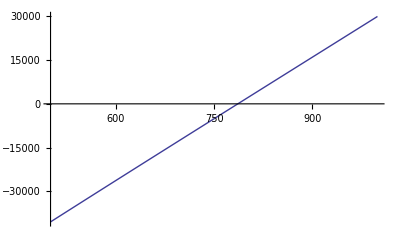

```mathematica
(* Example 8: Use the PET function -Dgr- to plot delta-G(R) of the reaction:
3 An = Gr + 2 Ky + Qz as function of T(K) for P = 10 kbar.  *)

phases = {gr,an,ky,qz}; (* define phase components in the list phases  *)
rea =MakeRea[phases] ;           (* calculate the reaction stoichiometry relating the phase components *)
Plot[Dgr[rea[[1]],10000,t,"None"][[1]],{t,500,1000}]
```

```mathematica
(* Example 9: Use the PET function -CalcRea- to calculate the reaction: 3 An = Gr + 2 Ky + Qz 
using th option: CalcReaMode -> TP (calculate equilibrium P for given T(C) ) *) 

phases = {gr,an,ky,qz}; (* define phase components in the list phases  *)
rea =MakeRea[phases];            (* calculate the reaction stoichiometry relating the phase components *)
result = CalcRea[rea,CalcReaMode->TP,CalcReaMin->500,CalcReaMax->700,Steps->21]
```

calculating PT data of the reaction:

{-3. an,1. gr,2. ky,1. qz}

9704.62 500.

9926.75 510.

10149.1 520.

10371.7 530.

10594.4 540.

10817.5 550.

11040.7 560.

11264.2 570.

11487.9 580.

11711.9 590.

11936.2 600.

12160.7 610.

12385.5 620.

12610.6 630.

12835.9 640.

13061.6 650.

13287.5 660.

13513.7 670.

13740.3 680.

13967.1 690.

14194.3 700.

{{{{-3. an,1. gr,2. ky,1. qz},{a(an)=1, a(gr)=1, a(ky)=1, a(qz)=1},{{500.,9704.62},{510.,9926.75},{520.,10149.1},{530.,10371.7},{540.,10594.4},{550.,10817.5},{560.,11040.7},{570.,11264.2},{580.,11487.9},{590.,11711.9},{600.,11936.2},{610.,12160.7},{620.,12385.5},{630.,12610.6},{640.,12835.9},{650.,13061.6},{660.,13287.5},{670.,13513.7},{680.,13740.3},{690.,13967.1},{700.,14194.3}}}},{Dataset -> B88,SampleFile->None}}

```mathematica
(* Example 10 (for Berman data set only): 
Calculations for mafic gneiss sample MG-20, Mäder et al. (1994): Can J Earth Sci, 31, 1134-1145;
This example calculates reactions (1)-(7) cited in this paper and plots Fig.3 of this paper;
See example 11 how to modify this raw plot in order to get a publication ready figure;
 *) 
(* sample from Percival (1983): Am Min 68: 667-686  *) 
(* below are the mineral analyses for phases in MG-20; copy these into a file
and calculate the mineral formulae and produce a *.cmp file (see CalcFormula::usage);
Correct the plagioclase data in the *.cmp file as follows (for unknown reasons CMP.EXE produces ***** for plag);
PLAG [-An-][-Ab-][-Or-]
 PLAG .3360 .6640 0.0000   
*)
(*
Label Mineral SiO2 TiO2 Al2O3 Cr2O3 FeO MnO MgO CaO Na2O K2O
1 grt 38.01 0 20.99 0.22 28.06 0.7 4.11 8.32 0.27 0
2 cpx 51.57 0.34 2.92 0.21 11.81 0 11.34 22.65 0.74 0.08
3 opx 49.06 0.03 4.75 0.34 31.2 0.81 13.35 1.39 0.52 0
4 amph 42.29 2.03 12.98 0.08 18.43 0.17 9.28 11.41 1.95 0.69
5 plag 59.82 0 25.45 0 0 0 0 7.04 7.69 0
*)
(* Example 10: formula calculation  *)
CalcFormula["Pmg20",CalcFormulaMode->{}];
```

Message from -CalcFormula-: creating file "Pmg20.fu".

{{-4. gr,-2. py,-12. qz,-3. ts,12. an,3. tr}}

{{-3. ab,-6. an,-3. tr,2. gr,3. prg,1. py,18. qz}}

{{-2. di,-2. qz,-1. ts,2. an,1. tr}}

{{-1. di,-1. prg,-5. qz,1. ab,1. an,1. tr}}

{{-5. alm,-3. tr,3. fact,5. py}}

{{-1. alm,-1. ts,1. fts,1. py}}

{{-4. alm,-3. prg,3. fprg,4. py}}

calculating PT data of the reaction:

{-4. gr,-2. py,-12. qz,-3. ts,12. an,3. tr}

calculating PT data of the reaction:

{-3. ab,-6. an,-3. tr,2. gr,3. prg,1. py,18. qz}

calculating PT data of the reaction:

{-2. di,-2. qz,-1. ts,2. an,1. tr}

calculating PT data of the reaction:

{-1. di,-1. prg,-5. qz,1. ab,1. an,1. tr}

calculating PT data of the reaction:

{-5. alm,-3. tr,3. fact,5. py}

calculating PT data of the reaction:

{-1. alm,-1. ts,1. fts,1. py}

calculating PT data of the reaction:

{-4. alm,-3. prg,3. fprg,4. py}

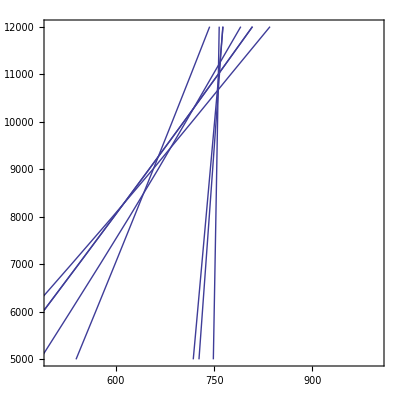

```mathematica
(* Example 10 continued: reaction calculation  *)
Dataset[Dataset-> B88]; 
file = "Pmg20";
phases1 = {ts,py,gr,qz,tr,an};
phases2= {tr,an,ab,qz,gr,py,prg};
phases3 = {ts,di,qz,tr,an};
phases4 = {prg,di,qz,tr,an,ab};
phases5 = {alm,py,tr,fact};
phases6 = {alm,py,ts,fts};
phases7 = {prg,fprg,alm,py};
rea1 = MakeRea[phases1]
rea2 = MakeRea[phases2]
rea3 = MakeRea[phases3]
rea4 = MakeRea[phases4]
rea5 = MakeRea[phases5]
rea6 = MakeRea[phases6]
rea7 = MakeRea[phases7]
r1=CalcRea[rea1,CalcReaMode->PT,CalcReaMin->5000,CalcReaMax->12000,Steps->8,Screen->ScreenNo,SampleFile->file];
r2=CalcRea[rea2,Screen->ScreenNo,SampleFile->file];
r3=CalcRea[rea3,Screen->ScreenNo,SampleFile->file];
r4=CalcRea[rea4,Screen->ScreenNo,SampleFile->file];
r5=CalcRea[rea5,Screen->ScreenNo,SampleFile->file];
r6=CalcRea[rea6,Screen->ScreenNo,SampleFile->file];
r7=CalcRea[rea7,Screen->ScreenNo,SampleFile->file];
plot=PlotRea[Join[r1[[1]],r2[[1]],r3[[1]],r4[[1]],r5[[1]],r6[[1]],r7[[1]]]];
Show[plot,PlotRange->{{500,1000},{5000,12000}},Frame->True,AspectRatio->1]
```

{{-6. an,-3. fprg,-3. py,-6. qz,3. ab,4. alm,2. gr,3. ts},{-3. fprg,-2. gr,-5. py,-18. qz,3. ab,4. alm,6. an,3. tr},{-3. fprg,-4. py,4. alm,3. prg},{-6. an,-3. fprg,-6. qz,3. ab,1. alm,3. fts,2. gr},{-1. alm,-3. fprg,-2. gr,-18. qz,3. ab,6. an,3. fact},{-2. gr,-1. py,-3. qz,3. an,3. di}}

calculating PT data of the reaction:

{-6. an,-3. fprg,-3. py,-6. qz,3. ab,4. alm,2. gr,3. ts}

calculating PT data of the reaction:

{-3. fprg,-2. gr,-5. py,-18. qz,3. ab,4. alm,6. an,3. tr}

calculating PT data of the reaction:

{-3. fprg,-4. py,4. alm,3. prg}

calculating PT data of the reaction:

{-6. an,-3. fprg,-6. qz,3. ab,1. alm,3. fts,2. gr}

calculating PT data of the reaction:

{-1. alm,-3. fprg,-2. gr,-18. qz,3. ab,6. an,3. fact}

calculating PT data of the reaction:

{-2. gr,-1. py,-3. qz,3. an,3. di}

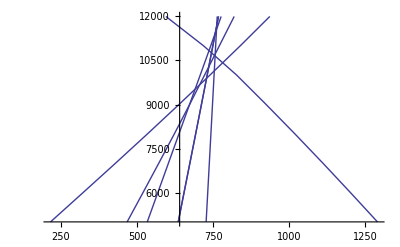

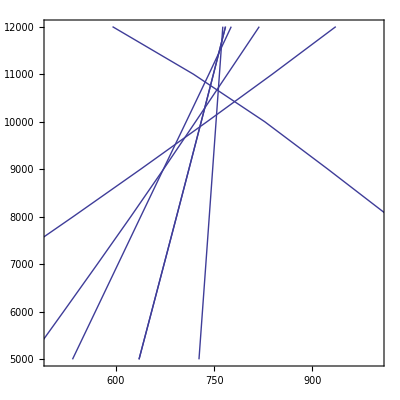

```mathematica
(* Example 11: same example as 10, but now only linearly independent reactions are calculated from the set of phase components  *)
(* The PET function -CalcReaIntersection- is then used to calculate all intersections and the Mathematica built-in functions
-Mean- and -StandardDeviation-
are used to calculate mean and standard deviation of P and T for this sample from the intersections of linearly independent reactions.  *)
Dataset[Dataset-> B88]; file = "Pmg20";
phases ={qz,alm,py,gr,an,ab,di,fprg,fact,fts,prg,tr,ts};
rea = MakeRea[phases]
result=CalcRea[rea,CalcReaMin->5000,CalcReaMax->12000,Steps->8,SampleFile->file,Screen->ScreenNo];
plot=PlotRea[result]
Show[plot,PlotRange->{{500,1000},{5000,12000}},Frame->True,AspectRatio->1]
```

```mathematica
(* Example 11 continued: calculate reaction intersections and mean and std of P and T  *)
is=CalcReaIntersection[result] (* calculate reaction intersections  *)
{p,t,dummy}=Transpose[is];  (* p is now a list of all pressures, t of all temperatures  *)
Mean[p]
StandardDeviation[p]
Mean[t]
StandardDeviation[t]
```

{{10770.,744.833,{1,2}},{11689.3,761.883,{1,3}},{10665.,756.584,{2,3}},{11438.7,757.25,{1,4}},{10841.7,736.709,{2,4}},{11553.6,761.182,{3,4}},{10288.,735.836,{1,5}},{10680.,754.916,{2,5}},{10720.1,756.87,{3,5}},{8987.27,672.107,{4,5}},{9892.05,728.415,{1,6}},{10429.1,782.432,{2,6}},{10144.8,753.888,{3,6}},{9519.29,690.696,{4,6}},{9664.32,705.4,{5,6}}}

10485.5

765.06

739.934

29.7893

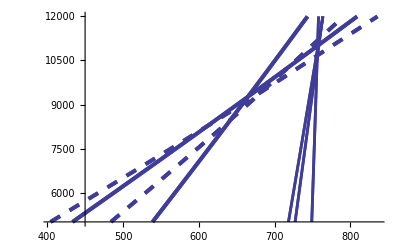

```mathematica
(* Example 12: modify a plot (reactions calculated before in example 10) by using options of -PlotRea- and -Show- *)
(* create the raw-plot: change thickness and dashing of reactions  *)
p1=PlotRea[r1,PlotReaStyle->{Thickness[0.007]},PlotReaMode->1];
p2=PlotRea[r2,PlotReaStyle->{Thickness[0.007],Dashing[{0.02,0.02}]},PlotReaMode->1];
p3=PlotRea[r3,PlotReaStyle->{Thickness[0.007]},PlotReaMode->1];
p4=PlotRea[r4,PlotReaStyle->{Thickness[0.007],Dashing[{0.02,0.02}]},PlotReaMode->1];
p5=PlotRea[r5,PlotReaStyle->{Thickness[0.005]},PlotReaMode->1];
p6=PlotRea[r6,PlotReaStyle->{Thickness[0.005]},PlotReaMode->1];
p7=PlotRea[r7,PlotReaStyle->{Thickness[0.005]},PlotReaMode->1];
plot = Show[p1,p2,p3,p4,p5,p6,p7,DisplayFunction->$DisplayFunction]
```

```mathematica
(*  ---------------------------------------    -CalcRea-  -----------------------------------------  *)
(*  ---------------------------------------  T-X(CO2) equilibria  -----------------------------------------  *)
(* Example 13: Use the PET function -CalcRea- to calculate the equilibrium 
5 Dol + 8 Qz + 1 H2O = 1 Tr + 3 Cal + 7 CO2 for pure phase components *) 
(* chose your data set (uncomment the corresponding) *)
(* Dataset[Dataset-> B88]; *)
(* Dataset[Dataset->HP32]; *)
(* Dataset[Dataset->G97]; *)

Dataset[Dataset->G97]; 
phases = {dol,qz,tr,cal,co2,h2o};
rea =MakeRea[phases] ; 
r1=CalcRea[rea,CalcReaMode->TXCO2,CalcReaMin->0.1,CalcReaMax->0.9,Steps->9,Screen->ScreenYes,SampleFile->"None"]
```

calculating T-X(CO2) data at 5000 bar of the reaction:

{-3. cal,-7. co2,-1. tr,5. dol,1. h2o,8. qz}

491.142 0.1

514.78 0.2

529.3 0.3

541.876 0.4

554.322 0.5

567.315 0.6

582.302 0.7

602.347 0.8

628.622 0.9

{{{{-3. cal,-7. co2,-1. tr,5. dol,1. h2o,8. qz},{a(cal)=1, a(co2)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(tr)=1, a(dol)=1, a(h2o)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(qz)=1},{{0.1,491.142},{0.2,514.78},{0.3,529.3},{0.4,541.876},{0.5,554.322},{0.6,567.315},{0.7,582.302},{0.8,602.347},{0.9,628.622}}}},{Dataset -> G97,SampleFile->None,PinTX->5000}}

```mathematica
(* Example 14: Use the PET function -CalcRea- to calculate the equilibrium 
5 Dol + 8 Qz + 1 H2O = 1 Tr + 3 Cal + 7 CO2 
using amphibole data from "ho2468.cmp" *) 

CalcFormula["ho2468",CalcFormulaMode->{}];
phases = {dol,qz,tr,cal,co2,h2o};
rea =MakeRea[phases] ; 
r1=CalcRea[rea,CalcReaMode->TXCO2,CalcReaMin->0.1,CalcReaMax->0.9,Steps->9,Screen->ScreenYes,SampleFile->"ho2468"]
```

Message from -CalcFormula-: creating file "ho2468.fu".

calculating T-X(CO2) data at 5000 bar of the reaction:

{-3. cal,-7. co2,-1. tr,5. dol,1. h2o,8. qz}

456.865 0.1

474.823 0.2

485.345 0.3

494.522 0.4

503.849 0.5

513.844 0.6

524.871 0.7

537.6 0.8

554.257 0.9

{{{{-3. cal,-7. co2,-1. tr,5. dol,1. h2o,8. qz},{a(cal)=1, a(co2)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(tr)=AmphMaederEtAl, a(dol)=1, a(h2o)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(qz)=1},{{0.1,456.865},{0.2,474.823},{0.3,485.345},{0.4,494.522},{0.5,503.849},{0.6,513.844},{0.7,524.871},{0.8,537.6},{0.9,554.257}}}},{Dataset -> G97,SampleFile->ho2468,PinTX->5000}}

```mathematica
(* Example 15: Use the PET function -CalcRea- to calculate the equilibrium 
5 Dol + 8 Qz + 1 H2O = 1 Tr + 3 Cal + 7 CO2: 
calculate the reaction for a(cal) = 0.86 and use the activity model for amphibole *) 
Dataset[Dataset-> B88]; 
phases = {dol,qz,tr,cal,co2,h2o};
rea =MakeRea[phases] ; 
rea={{rea[[1]],{0.86,1,"am",1,1,1}}};  
r1=CalcRea[rea,CalcReaMode->TXCO2,CalcReaMin->0.1,CalcReaMax->0.9,Steps->9]
```

calculating T-X(CO2) data at 5000 bar of the reaction:

{{-3. cal,-7. co2,-1. tr,5. dol,1. h2o,8. qz},{0.86,1,am,1,1,1}}

467.571 0.1

494.287 0.2

511.208 0.3

525.801 0.4

540.035 0.5

554.666 0.6

570.238 0.7

587.657 0.8

609.731 0.9

{{{{{-3. cal,-7. co2,-1. tr,5. dol,1. h2o,8. qz},{0.86,1,am,1,1,1}},{a(cal)=0.86, a(co2)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(tr)=0.1, a(dol)=1, a(h2o)={FluidActivityModel -> KerrickJacobs81, FluidSystem -> H2OCO2}, a(qz)=1},{{0.1,467.571},{0.2,494.287},{0.3,511.208},{0.4,525.801},{0.5,540.035},{0.6,554.666},{0.7,570.238},{0.8,587.657},{0.9,609.731}}}},{Dataset -> B88,SampleFile->None,PinTX->5000}}

Calculating reactions with 6 phases

(degree of freedom =  1 ): from combinatorics, there are 7 possible reactions.

Calculating reactions with 5 phases

(degree of freedom =  2 ): from combinatorics, there are 21 possible reactions.

Calculating reactions with 4 phases

(degree of freedom =  3 ): from combinatorics, there are 35 possible reactions.

Calculating reactions with 3 phases

(degree of freedom =  4 ): from combinatorics, there are 35 possible reactions.

Calculating reactions with 2 phases

(degree of freedom =  5 ): from combinatorics, there are 21 possible reactions.

{{-1. cal,-1. ma,-2. qz,2. an,1. co2,1. h2o},{-1. ma,-2. qz,-2. zo,5. an,2. h2o},{-3. an,-1. cal,-1. h2o,1. co2,2. zo},{-1. an,-2. cal,-1. ma,-2. qz,2. co2,2. zo},{-5. cal,-3. ma,-6. qz,5. co2,1. h2o,4. zo}}

calculating T-X(CO2) data at 5000 bar of the reaction:

{-1. cal,-1. ma,-2. qz,2. an,1. co2,1. h2o}

calculating T-X(CO2) data at 5000 bar of the reaction:

{-1. ma,-2. qz,-2. zo,5. an,2. h2o}

calculating T-X(CO2) data at 5000 bar of the reaction:

{-3. an,-1. cal,-1. h2o,1. co2,2. zo}

calculating T-X(CO2) data at 5000 bar of the reaction:

{-1. an,-2. cal,-1. ma,-2. qz,2. co2,2. zo}

calculating T-X(CO2) data at 5000 bar of the reaction:

{-5. cal,-3. ma,-6. qz,5. co2,1. h2o,4. zo}

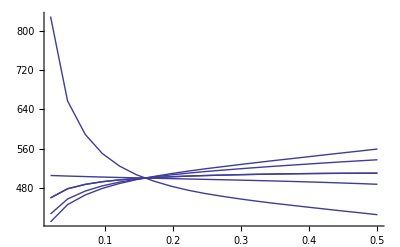

```mathematica
(* Example 16: Use the PET function -CalcRea- to calculate a T-X(CO2) diagram for the phases: {zo, an, ma, cal, qz, h2o, co2} *) 
phases = {zo, an, ma, cal, qz, h2o, co2};

rea =MakeRea[phases, MakeReaMode->1]  (* use option  MakeReaMode->1 to find all possible reactions  *)
r1=CalcRea[rea,CalcReaMode->TXCO2,CalcReaMin->0.02,CalcReaMax->0.5,Steps->20,Screen->ScreenNo,SampleFile->"None"];
PlotRea[r1]
```

```mathematica
(*  ---------------------------------------   -CalcRea-    -----------------------------------------  *)
(*  -------------------------- Redox reactions:  T-X(H2) and logf(O2)-T equilibria  -----------------------------------------  *)
(* Example 17: Use the PET function -CalcRea- to calculate a redox reaction: Ann = San + Mag + H2 *)
(* In this example T-X(H2) data are calculated *)

phases = {ann,san,mt,h2};
rea =MakeRea[phases];
r1=CalcRea[rea,CalcReaMode->TXH2,CalcReaMin->0.00005,CalcReaMax->0.005,Steps->10,Screen->ScreenYes,SampleFile->"None"]
```

calculating T-X(H2) data at 5000 bar of the reaction:

{-1. ann,1. h2,1. mt,1. san}

471.11 0.00005

648.899 0.0006

709.476 0.00115

750.468 0.0017

782.401 0.00225

808.988 0.0028

832.008 0.00335

852.458 0.0039

870.961 0.00445

887.929 0.005

{{{{-1. ann,1. h2,1. mt,1. san},{a(ann)=1, a(h2)={FluidActivityModel -> Holloway77, FluidSystem -> H2OH2}, a(mt)=1, a(san)=1},{{0.,471.11},{0.001,648.899},{0.001,709.476},{0.002,750.468},{0.002,782.401},{0.003,808.988},{0.003,832.008},{0.004,852.458},{0.004,870.961},{0.005,887.929}}}},{Dataset -> B88,SampleFile->None,PinTX->5000}}

{{-1. ann,1. h2,1. mt,1. san}}

{{{-1. ann,1. h2,1. mt,1. san},{0.8,1,1,1}}}

calculating logf(O2)-T data at 5000 bar of the reaction:

{{-1. ann,1. h2,1. mt,1. san},{0.8,1,1,1}}

calculating logfO2-T data at 5000 bar of the reaction:

{-6. hem,4. mt,1. o2}

{{{{-6. hem,4. mt,1. o2},{a(hem)=1, a(mt)=1, a(o2)=1},{{400.,-23.49},{422.222,-22.277},{444.444,-21.136},{466.667,-20.059},{488.889,-19.039},{511.111,-18.073},{533.333,-17.153},{555.556,-16.277},{577.778,-15.438},{600.,-14.635}}}},{Dataset -> B88,SampleFile->None}}

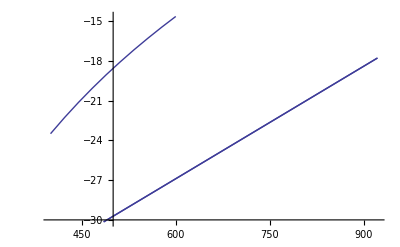

```mathematica
(* Example 18: Use the PET function -CalcRea- to calculate the redox reactions: 
Ann = San + Mag + H2 and the Hem/Mag buffer. Use a(ann) = 0.8 in the calculation *)
(* In this example logf(O2)-T data are calculated for Ann = San + Mag + H2 *)

phases = {ann,san,mt,h2};
rea =MakeRea[phases]
rea = {{rea[[1]],{0.8,1,1,1}}}
r1=CalcRea[rea,CalcReaMode->TXH2logfO2,CalcReaMin->0.00005,CalcReaMax->0.005,Steps->2,Screen->ScreenNo,SampleFile->"None"];
phases = {hem,mt,o2};
rea =MakeRea[phases];
r2=CalcRea[rea,CalcReaMode->logfO2T,CalcReaMin->400,CalcReaMax->600,Steps->10,Screen->ScreenNo,SampleFile->"None"]
PlotRea[Join[r1[[1]],r2[[1]]]]
```

calculating logfO2-T data at 5000 bar of the reaction:

{-2. mt,-3. qz,3. fa,1. o2}

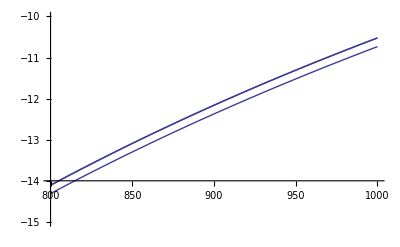

```mathematica
(* Example 19: Use the PET function -CalcRea- to calculate the QFM buffer reaction: 
Compare this to results from the PET function -O2buffers- *)
phases={qz,fa,mt,o2}; rea=MakeRea[phases]; r1=CalcRea[rea,CalcReaMode->logfO2T,CalcReaMin->800,CalcReaMax->1000,Steps->21,Screen->ScreenNo,SampleFile->"None"]; plot1=PlotRea[r1]; plot2=Plot[O2buffers[5000,t+273.15,Buffer->QFM]⟦3⟧,{t,800,1000}]; Show[plot1,plot2,PlotRange->{{800,1000},{-15,-10}}]
```

```mathematica
(*  ---------------------------------------   -MakeRea-     -----------------------------------------  *)
(* display the usage for the PET-functions -MakeRea-  *)
 
MakeRea::usage
```

MakeRea[{list_of_phase_components}]
calculates for a user-defined list of phase components the reactions that can be
written among them (abbreviations as shown by MinList[] must be used).
The following option is available with -MakeRea-:

Name           value          meaning

MakeReaMode -> 0 (default)    calculate a set of linearly independent reactions
               1              calculate all possible reactions (search algorithm)
               2              calculate all possible reactions (algorithm of
                              Powell (1990), Contrib Mineral Petrol 106:61-65)

Calculating all possible reactions: The search algorithm (MakeReaMode -> 1) works somewhat
slowlier than the algorithm of Powell (1990) (MakeReaMode -> 2), but the latter may not find
all reactions in cases where colinearities exists between phase components.
ReturnValue: {reaction 1, reaction 2,...},
where each reaction is a list of the form: {sc1*pc1, sc2*pc2, sc3*pc3, ...}
(sc = stoichiometric coefficient in the reaction, pc = phase component-abbreviation).

Example:
phases = {ann, phl, alm, py, gr, an, qz, sil};
rea = MakeRea[phases]
{{-3. an, 1. gr, 1. qz, 2. sil}, {-1. alm, -1. phl, 1. ann, 1. py}}

This returns the GASP-reaction and the grt-bt thermometer as linearly independent reactions.
See PET_CalcRea.nb for more examples.
Called from: User.
Calls: -MakeCompositionMatrix-, -NullSpace-.
Package name: UTILITY.m
PET: Petrological Elementary Tools, (c) Edgar Dachs.

```mathematica
(* Example 20: Use the PET function -MakeCompositionMatrix- to calculate the composition matrix of the
phases mu, qz, san, ky and h2o. *) 

phases={mu,qz,san,ky,h2o};
{matrix, elements} = MakeCompositionMatrix[phases]
MatrixForm[matrix]
```

{{{3,0,1,2,0},{2,0,0,0,2},{1,0,1,0,0},{12,2,8,5,1},{3,1,3,1,0}},{AL,H,K,O,SI}}

(3 | 0 | 1 | 2 | 0
2 | 0 | 0 | 0 | 2
1 | 0 | 1 | 0 | 0
12 | 2 | 8 | 5 | 1
3 | 1 | 3 | 1 | 0)

```mathematica
(* Example 21: Use the PET function -MakeRea- to calculate a linearly independent set of reactions for the phase components: {ann,phl,alm,py,gr,an,qz,sil}  *)

phases={ann,phl,alm,py,gr,an,qz,sil};
rea=MakeRea[phases]
```

{{-3. an,1. gr,1. qz,2. sil},{-1. alm,-1. phl,1. ann,1. py}}

```mathematica
(* Example 22: Use the PET function -MakeRea- to calculate all possible reactions for the phase components: {dsp,qz,ky,kao,pyp,zo,ma,gr,an,h2o,law}  *)

phases ={dsp,qz,ky,kao,pyp,zo,ma,gr,an,h2o,law};
r1=MakeRea[phases,MakeReaMode->1]
```

Calculating reactions with 5 phases

(degree of freedom =  1 ): from combinatorics, there are 462 possible reactions.

Calculating reactions with 4 phases

(degree of freedom =  2 ): from combinatorics, there are 330 possible reactions.

Calculating reactions with 3 phases

(degree of freedom =  3 ): from combinatorics, there are 165 possible reactions.

Calculating reactions with 2 phases

(degree of freedom =  4 ): from combinatorics, there are 55 possible reactions.

{{-2. dsp,-2. gr,-3. kao,6. an,7. h2o},{-3. gr,-1. kao,-7. ky,9. an,4. dsp},{-1. gr,-1. kao,-1. ky,3. an,2. h2o},{-2. dsp,-1. kao,3. h2o,2. ky},{-3. an,-2. dsp,1. gr,1. h2o,3. ky},{-1. an,-2. h2o,1. law},{-1. gr,-1. kao,-1. ky,2. an,1. law},{-7. an,-4. dsp,2. gr,6. ky,1. law},{-1. gr,-7. h2o,-3. ky,2. dsp,3. law},{-1. gr,-4. h2o,-1. kao,-1. ky,3. law},{-3. an,-4. dsp,-2. kao,4. ky,3. law},{-2. dsp,-2. gr,-5. h2o,-3. kao,6. law},{-4. dsp,-4. gr,-6. kao,5. an,7. law},{-8. dsp,-3. gr,-7. kao,5. ky,9. law},{-9. ma,14. dsp,3. gr,1. kao,7. ky},{-7. ma,10. dsp,2. gr,6. ky,1. law},{-1. gr,-5. kao,-4. ma,7. ky,7. law},{-3. ma,4. dsp,1. gr,1. h2o,3. ky},{-2. kao,-3. ma,1. gr,7. h2o,7. ky},{-2. kao,-3. ma,2. dsp,4. ky,3. law},{-5. an,-2. ma,2. gr,6. ky,1. law},{-1. an,-2. kao,-2. ma,4. ky,3. law},{-4. gr,-6. kao,-2. ma,7. an,7. law},{-1. ma,1. an,2. dsp},{-2. gr,-3. kao,-1. ma,7. an,7. h2o},{-1. kao,-1. ma,1. an,3. h2o,2. ky},{-2. an,-1. ma,1. gr,1. h2o,3. ky},{-2. h2o,-1. ma,2. dsp,1. law},{-1. kao,-1. ma,1. h2o,2. ky,1. law},{-2. gr,-7. h2o,-3. kao,-1. ma,7. law},{-1. gr,-5. h2o,-3. ky,2. law,1. ma},{-3. gr,-1. kao,-7. ky,7. an,2. ma},{-14. dsp,-4. gr,-6. kao,7. law,5. ma},{-14. dsp,-2. gr,-3. kao,7. h2o,6. ma},{-18. dsp,-4. gr,-7. pyp,12. an,8. kao},{-34. dsp,-4. gr,-7. pyp,16. ky,12. law},{-15. ma,-7. pyp,5. gr,11. kao,21. ky},{-4. gr,-9. ma,-7. pyp,21. an,8. kao},{-17. ma,-5. pyp,2. gr,26. ky,11. law},{-10. dsp,-4. gr,-3. pyp,12. an,8. h2o},{-10. dsp,-4. gr,-3. pyp,8. an,4. law},{-10. dsp,-4. gr,-16. h2o,-3. pyp,12. law},{-4. gr,-5. ma,-3. pyp,17. an,8. h2o},{-5. ma,-3. pyp,5. an,4. kao,4. ky},{-4. gr,-5. ma,-3. pyp,13. an,4. law},{-4. gr,-26. h2o,-5. ma,-3. pyp,17. law},{-26. dsp,-4. gr,-3. pyp,4. law,8. ma},{-34. dsp,-4. gr,-3. pyp,8. h2o,12. ma},{-5. gr,-9. ky,-2. pyp,15. an,1. kao},{-6. gr,-10. ky,-2. pyp,17. an,1. law},{-9. ma,-2. pyp,3. gr,11. h2o,17. ky},{-4. gr,-8. ky,-1. pyp,12. an,2. dsp},{-3. gr,-5. ky,-1. pyp,9. an,1. h2o},{-6. dsp,-1. pyp,4. h2o,4. ky},{-2. an,-6. dsp,-1. pyp,4. ky,2. law},{-3. gr,-17. h2o,-5. ky,-1. pyp,9. law},{-2. kao,-5. ma,-1. pyp,8. ky,5. law},{-3. ma,-1. pyp,3. an,4. h2o,4. ky},{-3. ma,-1. pyp,1. an,4. ky,2. law},{-2. h2o,-3. ma,-1. pyp,4. ky,3. law},{-2. dsp,-2. ma,-1. pyp,4. ky,2. law},{-4. h2o,-1. ma,-1. pyp,2. kao,1. law},{-4. gr,-8. ky,-1. pyp,11. an,1. ma},{-2. gr,-5. kao,6. an,9. h2o,1. pyp},{-2. kao,2. dsp,2. h2o,1. pyp},{-3. kao,5. h2o,2. ky,1. pyp},{-1. an,-2. kao,2. dsp,1. law,1. pyp},{-2. gr,-3. h2o,-5. kao,6. law,1. pyp},{-12. ma,22. dsp,4. gr,8. ky,1. pyp},{-2. kao,-1. ma,4. dsp,1. law,1. pyp},{-1. an,-2. kao,2. h2o,1. ma,1. pyp},{-2. an,-2. kao,1. law,1. ma,1. pyp},{-5. an,-6. kao,4. ky,5. law,2. pyp},{-4. gr,-10. kao,3. an,9. law,2. pyp},{-4. kao,-4. ky,10. dsp,3. pyp},{-5. gr,-17. kao,3. ky,15. law,4. pyp},{-4. gr,-16. kao,6. dsp,12. law,5. pyp},{-8. kao,-12. ma,42. dsp,4. gr,7. pyp},{-8. gr,-26. kao,21. law,3. ma,7. pyp},{-2. gr,-17. kao,21. h2o,6. ma,7. pyp},{-2. kao,-3. ma,-21. qz,1. gr,7. pyp},{-3. ma,-11. qz,1. gr,2. ky,3. pyp},{-2. kao,-1. ma,-8. qz,1. law,3. pyp},{-8. dsp,-1. gr,-7. qz,3. an,2. kao},{-12. dsp,-1. gr,-7. qz,4. ky,3. law},{-6. ma,-7. qz,2. gr,3. kao,7. ky},{-1. gr,-4. ma,-7. qz,7. an,2. kao},{-6. ma,-5. qz,1. gr,8. ky,3. law},{-1. kao,-1. ky,-5. qz,2. pyp},{-2. dsp,-4. qz,1. pyp},{-1. ma,-4. qz,1. an,1. pyp},{-2. h2o,-1. ma,-4. qz,1. law,1. pyp},{-1. an,-2. kao,-4. qz,1. law,2. pyp},{-4. dsp,-1. gr,-3. qz,3. an,2. h2o},{-4. dsp,-3. qz,1. kao,1. ky},{-4. dsp,-1. gr,-3. qz,2. an,1. law},{-4. dsp,-1. gr,-4. h2o,-3. qz,3. law},{-1. gr,-2. ma,-3. qz,5. an,2. h2o},{-2. ma,-3. qz,2. an,1. kao,1. ky},{-1. gr,-2. ma,-3. qz,4. an,1. law},{-1. gr,-8. h2o,-2. ma,-3. qz,5. law},{-8. dsp,-1. gr,-3. qz,1. law,2. ma},{-10. dsp,-1. gr,-3. qz,2. h2o,3. ma},{-1. gr,-4. kao,-3. qz,3. law,2. pyp},{-1. an,-4. dsp,-2. qz,2. ky,1. law},{-3. ma,-2. qz,1. gr,3. h2o,5. ky},{-2. ma,-2. qz,1. an,2. ky,1. law},{-3. h2o,-1. ma,-2. qz,1. kao,1. law},{-2. dsp,-1. ma,-2. qz,2. ky,1. law},{-1. kao,-2. qz,1. h2o,1. pyp},{-1. gr,-2. ky,-1. qz,3. an},{-2. dsp,-1. qz,1. h2o,1. ky},{-1. gr,-6. h2o,-2. ky,-1. qz,3. law},{-1. kao,-2. ma,-1. qz,3. ky,2. law},{-1. ma,-1. qz,1. an,1. h2o,1. ky},{-1. h2o,-1. ma,-1. qz,1. ky,1. law},{-1. gr,-2. kao,3. an,4. h2o,1. qz},{-1. kao,2. h2o,1. ky,1. qz},{-1. an,-1. kao,1. ky,1. law,1. qz},{-1. gr,-2. kao,1. an,2. law,1. qz},{-1. gr,-2. h2o,-2. kao,3. law,1. qz},{-3. ma,6. dsp,1. gr,2. ky,1. qz},{-1. kao,2. dsp,1. h2o,2. qz},{-1. gr,-3. kao,1. ky,3. law,2. qz},{-1. an,-1. kao,1. h2o,1. ma,2. qz},{-1. ma,-1. pyp,2. ky,1. law,2. qz},{-1. pyp,1. h2o,1. ky,3. qz},{-1. an,-2. kao,4. dsp,1. law,4. qz},{-2. kao,-1. ma,6. dsp,1. law,4. qz},{-3. an,-2. kao,1. law,2. ma,4. qz},{-1. gr,-4. kao,4. dsp,3. law,5. qz},{-1. gr,-2. pyp,3. an,2. h2o,5. qz},{-1. gr,-2. pyp,2. an,1. law,5. qz},{-1. gr,-4. h2o,-2. pyp,3. law,5. qz},{-1. an,-2. pyp,2. ky,1. law,6. qz},{-2. kao,-3. ma,14. dsp,1. gr,7. qz},{-3. gr,-8. kao,7. law,2. ma,7. qz},{-1. gr,-5. kao,7. h2o,3. ma,7. qz},{-1. gr,-4. pyp,3. an,2. kao,9. qz},{-1. gr,-4. pyp,1. law,2. ma,13. qz},{-1. gr,-6. pyp,4. ky,3. law,17. qz},{-1. gr,-5. pyp,2. h2o,3. ma,17. qz},{-2. kao,-42. zo,22. gr,18. ma,7. pyp},{-34. zo,20. gr,22. ky,8. law,1. pyp},{-1. pyp,-30. zo,20. gr,8. kao,18. ky},{-22. zo,12. gr,2. ky,8. ma,3. pyp},{-18. zo,12. gr,8. h2o,14. ky,1. pyp},{-14. zo,9. gr,3. kao,7. ky,1. ma},{-14. zo,7. an,6. gr,2. kao,3. ma},{-4. kao,-12. zo,18. dsp,8. gr,5. pyp},{-1. qz,-12. zo,8. gr,3. kao,7. ky},{-12. zo,7. gr,8. ky,3. law,1. qz},{-1. ma,-10. zo,6. gr,8. ky,3. law},{-6. ky,-3. pyp,-10. zo,20. an,4. kao},{-1. pyp,-10. zo,14. an,2. gr,6. h2o},{-1. pyp,-10. zo,11. an,2. gr,3. law},{-22. h2o,-1. pyp,-10. zo,2. gr,14. law},{-12. kao,-22. ky,-10. zo,20. ma,9. pyp},{-9. zo,1. dsp,6. gr,2. kao,5. ky},{-8. zo,5. gr,1. kao,5. ky,1. law},{-8. zo,4. an,6. dsp,4. gr,1. pyp},{-8. zo,1. an,4. gr,3. ma,1. pyp},{-2. dsp,-8. zo,4. gr,4. ma,1. pyp},{-14. kao,-8. zo,11. law,5. ma,5. pyp},{-3. qz,-8. zo,7. an,3. gr,2. kao},{-7. zo,5. an,3. dsp,3. gr,1. kao},{-1. dsp,-7. zo,4. gr,5. ky,2. law},{-7. dsp,-7. zo,3. gr,1. kao,5. ma},{-6. zo,4. gr,1. h2o,1. kao,4. ky},{-6. zo,5. an,2. dsp,2. gr,1. law},{-6. zo,5. an,2. gr,2. h2o,1. ma},{-6. zo,4. an,2. gr,1. law,1. ma},{-8. h2o,-6. zo,2. gr,5. law,1. ma},{-8. dsp,-6. zo,2. gr,1. law,5. ma},{-1. pyp,-6. zo,6. an,2. gr,2. kao},{-2. ky,-1. pyp,-6. zo,12. an,4. h2o},{-2. ky,-1. pyp,-6. zo,10. an,2. law},{-20. h2o,-2. ky,-1. pyp,-6. zo,12. law},{-6. zo,4. dsp,4. gr,2. ky,1. pyp},{-2. kao,-18. qz,-6. zo,4. gr,7. pyp},{-8. qz,-6. zo,4. gr,2. ky,3. pyp},{-6. zo,4. gr,3. h2o,5. ky,1. qz},{-8. kao,-6. zo,7. law,5. ma,10. qz},{-4. zo,1. an,2. gr,2. ky,1. law},{-2. kao,-4. zo,5. an,3. law},{-1. ma,-4. zo,3. gr,3. h2o,5. ky},{-10. dsp,-2. kao,-4. zo,3. law,5. ma},{-6. dsp,-3. pyp,-4. zo,8. an,4. kao},{-3. ma,-3. pyp,-4. zo,11. an,4. kao},{-22. dsp,-3. pyp,-4. zo,4. kao,8. ma},{-2. dsp,-1. pyp,-4. zo,8. an,4. h2o},{-2. dsp,-1. pyp,-4. zo,6. an,2. law},{-2. dsp,-12. h2o,-1. pyp,-4. zo,8. law},{-1. ma,-1. pyp,-4. zo,9. an,4. h2o},{-1. ma,-1. pyp,-4. zo,7. an,2. law},{-14. h2o,-1. ma,-1. pyp,-4. zo,9. law},{-14. dsp,-1. pyp,-4. zo,2. law,6. ma},{-18. dsp,-1. pyp,-4. zo,4. h2o,8. ma},{-12. kao,-4. zo,10. dsp,8. law,5. pyp},{-3. ky,-3. qz,-4. zo,8. an,1. kao},{-2. ky,-2. qz,-4. zo,7. an,1. law},{-1. qz,-4. zo,5. an,1. gr,2. h2o},{-1. qz,-4. zo,4. an,1. gr,1. law},{-8. h2o,-1. qz,-4. zo,1. gr,5. law},{-7. kao,-4. zo,5. ky,8. law,5. qz},{-3. kao,-7. ky,-4. zo,8. ma,9. qz},{-3. zo,3. an,1. dsp,1. gr,1. h2o},{-1. dsp,-3. zo,2. gr,2. h2o,3. ky},{-5. h2o,-3. zo,1. dsp,1. gr,3. law},{-5. dsp,-4. kao,-3. zo,5. ky,6. law},{-5. dsp,-3. zo,1. gr,1. h2o,3. ma},{-3. zo,3. dsp,2. gr,1. ky,2. qz},{-1. kao,-3. zo,7. dsp,2. gr,5. qz},{-1. kao,-2. zo,4. an,3. h2o},{-2. zo,1. an,1. gr,1. h2o,1. ky},{-1. h2o,-2. zo,1. gr,1. ky,1. law},{-5. h2o,-1. kao,-2. zo,4. law},{-6. kao,-5. ma,-2. zo,10. ky,9. law},{-2. ky,-2. zo,3. an,1. ma},{-6. h2o,-2. ky,-2. zo,3. law,1. ma},{-8. dsp,-1. kao,-2. zo,3. h2o,4. ma},{-4. kao,-2. zo,2. ky,4. law,1. pyp},{-9. kao,-2. zo,11. h2o,4. ma,4. pyp},{-6. kao,-10. qz,-2. zo,4. law,5. pyp},{-3. ma,-6. qz,-2. zo,7. an,2. kao},{-2. ky,-4. qz,-2. zo,4. an,1. pyp},{-3. qz,-2. zo,1. an,1. gr,1. pyp},{-2. dsp,-2. qz,-2. zo,3. an,1. law},{-1. ma,-2. qz,-2. zo,5. an,2. h2o},{-1. ma,-2. qz,-2. zo,4. an,1. law},{-8. h2o,-1. ma,-2. qz,-2. zo,5. law},{-8. dsp,-2. qz,-2. zo,1. law,3. ma},{-1. ky,-1. qz,-2. zo,4. an,1. h2o},{-7. h2o,-1. ky,-1. qz,-2. zo,4. law},{-2. zo,1. an,2. dsp,1. gr,1. qz},{-2. zo,1. gr,1. ma,1. qz},{-1. pyp,-2. zo,4. an,2. h2o,2. qz},{-1. pyp,-2. zo,3. an,1. law,2. qz},{-6. h2o,-1. pyp,-2. zo,4. law,2. qz},{-3. pyp,-2. zo,4. an,2. kao,6. qz},{-5. kao,-2. zo,7. h2o,4. ma,8. qz},{-2. ky,-3. pyp,-2. zo,4. ma,12. qz},{-4. pyp,-2. zo,1. law,3. ma,14. qz},{-5. pyp,-2. zo,2. h2o,4. ma,18. qz},{-7. pyp,-2. zo,6. ky,4. law,20. qz},{-7. pyp,-2. zo,2. kao,4. ma,22. qz},{-1. ky,-1. zo,2. an,1. dsp},{-4. h2o,-1. ky,-1. zo,1. dsp,2. law},{-3. dsp,-1. ky,-1. zo,2. ma},{-5. dsp,-1. pyp,-1. zo,3. ky,2. law},{-7. dsp,-4. qz,-1. zo,3. ky,2. law},{-3. dsp,-3. qz,-1. zo,2. an,1. kao},{-7. dsp,-3. qz,-1. zo,1. kao,2. ma},{-1. dsp,-1. qz,-1. zo,2. an,1. h2o},{-1. dsp,-3. h2o,-1. qz,-1. zo,2. law},{-5. dsp,-1. qz,-1. zo,1. h2o,2. ma},{-3. kao,-1. zo,5. dsp,2. law,5. qz},{-1. dsp,-1. gr,-1. kao,1. law,1. zo},{-3. kao,-4. ma,9. h2o,8. ky,2. zo},{-10. ma,-3. pyp,14. ky,6. law,2. zo},{-4. gr,-6. ky,-1. pyp,8. an,2. zo},{-4. ma,-1. pyp,4. h2o,6. ky,2. zo},{-7. ma,-6. qz,8. ky,3. law,2. zo},{-4. ma,-3. qz,3. h2o,5. ky,2. zo},{-5. dsp,-2. gr,-3. qz,1. h2o,3. zo},{-3. gr,-1. kao,-3. ky,1. an,4. zo},{-8. dsp,-3. gr,-5. qz,1. law,4. zo},{-5. gr,-8. kao,7. law,5. qz,4. zo},{-3. gr,-4. pyp,1. law,11. qz,4. zo},{-4. dsp,-4. gr,-3. kao,5. h2o,6. zo},{-4. gr,-7. kao,9. h2o,2. pyp,6. zo},{-10. gr,-22. kao,18. law,5. pyp,6. zo},{-4. gr,-5. kao,7. h2o,4. qz,6. zo},{-4. gr,-5. pyp,2. h2o,14. qz,6. zo},{-14. dsp,-8. gr,-3. pyp,4. h2o,12. zo},{-10. gr,-8. kao,-5. ma,7. law,14. zo},{-8. gr,-5. kao,-4. ma,7. h2o,14. zo},{-22. dsp,-12. gr,-5. pyp,4. law,16. zo},{-14. gr,-11. ma,-4. pyp,1. law,26. zo},{-18. gr,-14. ma,-5. pyp,2. h2o,34. zo}}

```mathematica
(* Example 23: Use the PET function -MakeRea- to calculate all possible reactions for the phase components {dsp,qz,ky,kao,pyp,zo,ma,gr,an,h2o,law} using the algorithm of Powell (1990)  *)

phases ={dsp,qz,ky,kao,pyp,zo,ma,gr,an,h2o,law};
r2=MakeRea[phases,MakeReaMode->2]
```

Warning from -MakeRea-: singular matrix occurred during calculation. Not all reactions may have been found.

Use option MakeReaMode -> 1 to find all reactions.

{{-34. dsp,-4. gr,-7. pyp,16. ky,12. law},{-22. dsp,-12. gr,-5. pyp,4. law,16. zo},{-18. dsp,-8. gr,-5. pyp,4. kao,12. zo},{-14. dsp,-4. gr,-6. kao,7. law,5. ma},{-8. dsp,-3. gr,-5. qz,1. law,4. zo},{-8. dsp,-3. gr,-7. kao,5. ky,9. law},{-7. dsp,-4. gr,-2. pyp,2. h2o,6. zo},{-4. an,-6. dsp,-4. gr,-1. pyp,8. zo},{-2. an,-6. dsp,-1. pyp,4. ky,2. law},{-5. dsp,-2. gr,-8. h2o,-2. pyp,6. law},{-5. dsp,-4. kao,-3. zo,5. ky,6. law},{-4. dsp,-1. gr,-4. h2o,-3. qz,3. law},{-4. dsp,-4. gr,-2. ky,-1. pyp,6. zo},{-4. dsp,-4. gr,-6. kao,5. an,7. law},{-3. an,-4. dsp,-2. kao,4. ky,3. law},{-7. an,-4. dsp,2. gr,6. ky,1. law},{-9. an,-4. dsp,3. gr,1. kao,7. ky},{-3. dsp,-2. gr,-1. ky,-2. qz,3. zo},{-5. an,-3. dsp,-3. gr,-1. kao,7. zo},{-1. an,-2. dsp,-1. gr,-1. qz,2. zo},{-2. dsp,-2. gr,-5. h2o,-3. kao,6. law},{-2. dsp,-12. h2o,-1. pyp,-4. zo,8. law},{-5. an,-2. dsp,-2. gr,-1. law,6. zo},{-2. dsp,-2. h2o,-1. pyp,2. kao},{-2. dsp,-2. ma,-1. pyp,4. ky,2. law},{-12. an,-2. dsp,4. gr,8. ky,1. pyp},{-1. dsp,-3. h2o,-1. qz,-1. zo,2. law},{-1. dsp,-6. gr,-2. kao,-5. ky,9. zo},{-1. dsp,-1. gr,-1. kao,1. law,1. zo},{-3. an,-1. dsp,-1. gr,-1. h2o,3. zo},{-2. an,-1. dsp,1. ky,1. zo},{-26. an,-1. dsp,-28. h2o,4. kao,1. ky,8. law,9. zo},{-8. ma,-9. qz,3. kao,7. ky,4. zo},{-7. h2o,-4. ma,-8. qz,5. kao,2. zo},{-7. h2o,-3. ma,-7. qz,1. gr,5. kao},{-4. an,-2. kao,-6. qz,3. pyp,2. zo},{-7. ma,-6. qz,8. ky,3. law,2. zo},{-3. an,-2. h2o,-5. qz,1. gr,2. pyp},{-6. ma,-5. qz,1. gr,8. ky,3. law},{-2. h2o,-1. ma,-4. qz,1. law,1. pyp},{-1. gr,-4. kao,-3. qz,3. law,2. pyp},{-1. gr,-8. h2o,-2. ma,-3. qz,5. law},{-8. h2o,-1. ma,-2. qz,-2. zo,5. law},{-4. an,-2. h2o,-2. qz,1. pyp,2. zo},{-3. an,-1. law,-2. qz,1. pyp,2. zo},{-3. h2o,-1. ma,-2. qz,1. kao,1. law},{-1. h2o,-1. ma,-2. qz,1. an,1. kao},{-7. gr,-8. ky,-3. law,-1. qz,12. zo},{-4. gr,-3. h2o,-5. ky,-1. qz,6. zo},{-1. gr,-6. h2o,-2. ky,-1. qz,3. law},{-7. h2o,-1. ky,-1. qz,-2. zo,4. law},{-2. h2o,-1. ky,-1. qz,1. kao},{-8. h2o,-1. qz,-4. zo,1. gr,5. law},{-1. gr,-1. ma,-1. qz,2. zo},{-3. an,-4. h2o,-1. qz,1. gr,2. kao},{-1. h2o,-1. ma,-1. qz,1. ky,1. law},{-1. kao,-2. ma,-1. qz,3. ky,2. law},{-20. gr,-22. ky,-8. law,-1. pyp,34. zo},{-20. gr,-8. kao,-18. ky,1. pyp,30. zo},{-3. gr,-11. h2o,-17. ky,9. ma,2. pyp},{-12. gr,-8. h2o,-14. ky,-1. pyp,18. zo},{-6. gr,-8. ky,-3. law,1. ma,10. zo},{-9. h2o,-8. ky,-2. zo,3. kao,4. ma},{-9. gr,-3. kao,-7. ky,-1. ma,14. zo},{-1. gr,-7. h2o,-7. ky,2. kao,3. ma},{-4. h2o,-6. ky,-2. zo,4. ma,1. pyp},{-5. gr,-1. kao,-5. ky,-1. law,8. zo},{-3. gr,-17. h2o,-5. ky,-1. pyp,9. law},{-3. gr,-3. h2o,-5. ky,1. ma,4. zo},{-5. an,-4. kao,-4. ky,5. ma,3. pyp},{-4. gr,-1. h2o,-1. kao,-4. ky,6. zo},{-3. an,-4. h2o,-4. ky,3. ma,1. pyp},{-3. gr,-1. kao,-3. ky,1. an,4. zo},{-1. gr,-5. h2o,-3. ky,2. law,1. ma},{-1. gr,-1. h2o,-3. ky,2. an,1. ma},{-12. gr,-2. ky,-8. ma,-3. pyp,22. zo},{-20. h2o,-2. ky,-1. pyp,-6. zo,12. law},{-6. h2o,-2. ky,-2. zo,3. law,1. ma},{-1. an,-2. gr,-2. ky,-1. law,4. zo},{-1. an,-3. h2o,-2. ky,1. kao,1. ma},{-5. h2o,-2. ky,-1. pyp,3. kao},{-1. gr,-4. h2o,-1. kao,-1. ky,3. law},{-1. gr,-1. kao,-1. ky,2. an,1. law},{-1. an,-1. gr,-1. h2o,-1. ky,2. zo},{-8. gr,-26. kao,21. law,3. ma,7. pyp},{-10. gr,-22. kao,18. law,5. pyp,6. zo},{-14. kao,-8. zo,11. law,5. ma,5. pyp},{-4. gr,-10. kao,3. an,9. law,2. pyp},{-10. gr,-8. kao,-5. ma,7. law,14. zo},{-21. an,-8. kao,4. gr,9. ma,7. pyp},{-4. gr,-6. kao,-2. ma,7. an,7. law},{-8. gr,-5. kao,-4. ma,7. h2o,14. zo},{-2. gr,-3. h2o,-5. kao,6. law,1. pyp},{-11. an,-4. kao,3. ma,3. pyp,4. zo},{-2. gr,-7. h2o,-3. kao,-1. ma,7. law},{-7. an,-6. gr,-2. kao,-3. ma,14. zo},{-2. an,-2. kao,1. law,1. ma,1. pyp},{-6. an,-2. gr,-2. kao,1. pyp,6. zo},{-5. h2o,-1. kao,-2. zo,4. law},{-18. gr,-14. ma,-5. pyp,2. h2o,34. zo},{-14. gr,-11. ma,-4. pyp,1. law,26. zo},{-4. gr,-26. h2o,-5. ma,-3. pyp,17. law},{-22. h2o,-1. pyp,-10. zo,2. gr,14. law},{-14. h2o,-1. ma,-1. pyp,-4. zo,9. law},{-1. an,-4. gr,-3. ma,-1. pyp,8. zo},{-8. h2o,-6. zo,2. gr,5. law,1. ma},{-1. an,-2. h2o,1. law},{-5. an,-2. gr,-2. h2o,-1. ma,6. zo},{-4. an,-2. gr,-1. law,-1. ma,6. zo},{-9. an,-4. h2o,1. ma,1. pyp,4. zo},{-7. an,-2. law,1. ma,1. pyp,4. zo},{-14. an,-2. gr,-6. h2o,1. pyp,10. zo},{-11. an,-2. gr,-3. law,1. pyp,10. zo},{-17. an,-8. h2o,4. gr,5. ma,3. pyp},{-13. an,-4. law,4. gr,5. ma,3. pyp},{-11. gr,-9. ma,-4. pyp,1. kao,21. zo},{-4. an,-3. h2o,1. kao,2. zo},{-4. h2o,-1. ma,-1. pyp,2. kao,1. law},{-2. h2o,-1. ma,-1. pyp,1. an,2. kao},{-5. an,-3. law,2. kao,4. zo},{-7. an,-7. h2o,2. gr,3. kao,1. ma},{-6. an,-9. h2o,-1. pyp,2. gr,5. kao},{-9. h2o,-2. pyp,-6. zo,4. gr,7. kao},{-11. h2o,-4. ma,-4. pyp,9. kao,2. zo},{-21. h2o,-6. ma,-7. pyp,2. gr,17. kao},{-1. h2o,-2. zo,1. gr,1. ky,1. law},{-3. an,-2. h2o,1. gr,1. kao,1. ky},{-4. kao,-2. zo,2. ky,4. law,1. pyp},{-1. kao,-1. ma,1. h2o,2. ky,1. law},{-3. an,-1. ma,2. ky,2. zo},{-12. an,-4. h2o,2. ky,1. pyp,6. zo},{-10. an,-2. law,2. ky,1. pyp,6. zo},{-5. gr,-17. kao,3. ky,15. law,4. pyp},{-5. an,-6. kao,4. ky,5. law,2. pyp},{-1. an,-2. kao,-2. ma,4. ky,3. law},{-2. h2o,-3. ma,-1. pyp,4. ky,3. law},{-3. ma,-1. pyp,1. an,4. ky,2. law},{-9. an,-1. h2o,3. gr,5. ky,1. pyp},{-20. an,-4. kao,6. ky,3. pyp,10. zo},{-5. an,-2. ma,2. gr,6. ky,1. law},{-8. an,-2. zo,4. gr,6. ky,1. pyp},{-1. gr,-5. kao,-4. ma,7. ky,7. law},{-7. an,-2. ma,3. gr,1. kao,7. ky},{-2. kao,-5. ma,-1. pyp,8. ky,5. law},{-11. an,-1. ma,4. gr,8. ky,1. pyp},{-15. an,-1. kao,5. gr,9. ky,2. pyp},{-6. kao,-5. ma,-2. zo,10. ky,9. law},{-17. an,-1. law,6. gr,10. ky,2. pyp},{-10. ma,-3. pyp,14. ky,6. law,2. zo},{-15. ma,-7. pyp,5. gr,11. kao,21. ky},{-20. ma,-9. pyp,12. kao,22. ky,10. zo},{-17. ma,-5. pyp,2. gr,26. ky,11. law},{-8. gr,-3. kao,-7. ky,1. qz,12. zo},{-1. an,-1. h2o,-1. ky,1. ma,1. qz},{-1. gr,-2. h2o,-2. kao,3. law,1. qz},{-1. gr,-2. kao,1. an,2. law,1. qz},{-5. an,-1. gr,-2. h2o,1. qz,4. zo},{-4. an,-1. gr,-1. law,1. qz,4. zo},{-1. an,-1. kao,1. ky,1. law,1. qz},{-4. an,-1. h2o,1. ky,1. qz,2. zo},{-3. an,1. gr,2. ky,1. qz},{-1. gr,-3. h2o,-5. ky,3. ma,2. qz},{-6. h2o,-1. pyp,-2. zo,4. law,2. qz},{-5. an,-2. h2o,1. ma,2. qz,2. zo},{-4. an,-1. law,1. ma,2. qz,2. zo},{-1. h2o,-1. pyp,1. kao,2. qz},{-1. gr,-3. kao,1. ky,3. law,2. qz},{-1. ma,-1. pyp,2. ky,1. law,2. qz},{-7. an,-1. law,2. ky,2. qz,4. zo},{-3. h2o,-5. ky,-2. zo,4. ma,3. qz},{-2. an,-1. kao,-1. ky,2. ma,3. qz},{-7. an,-3. gr,-2. kao,3. qz,8. zo},{-1. an,-1. gr,-1. pyp,3. qz,2. zo},{-5. an,-2. h2o,1. gr,2. ma,3. qz},{-4. an,-1. law,1. gr,2. ma,3. qz},{-8. an,-1. kao,3. ky,3. qz,4. zo},{-4. gr,-5. kao,7. h2o,4. qz,6. zo},{-3. an,-2. kao,1. law,2. ma,4. qz},{-1. an,-1. pyp,1. ma,4. qz},{-4. an,-1. pyp,2. ky,4. qz,2. zo},{-5. gr,-8. kao,7. law,5. qz,4. zo},{-1. gr,-4. h2o,-2. pyp,3. law,5. qz},{-1. gr,-2. pyp,2. an,1. law,5. qz},{-2. law,-3. pyp,3. kao,5. qz,1. zo},{-2. pyp,1. kao,1. ky,5. qz},{-7. kao,-4. zo,5. ky,8. law,5. qz},{-1. ky,-2. pyp,-1. zo,2. ma,6. qz},{-7. an,-2. kao,3. ma,6. qz,2. zo},{-1. an,-2. pyp,2. ky,1. law,6. qz},{-2. gr,-3. kao,-7. ky,6. ma,7. qz},{-3. gr,-8. kao,7. law,2. ma,7. qz},{-7. an,-2. kao,1. gr,4. ma,7. qz},{-4. gr,-2. ky,-3. pyp,8. qz,6. zo},{-1. law,-3. pyp,2. kao,1. ma,8. qz},{-1. gr,-4. pyp,3. an,2. kao,9. qz},{-8. kao,-6. zo,7. law,5. ma,10. qz},{-1. gr,-2. ky,-3. pyp,3. ma,11. qz},{-3. gr,-4. pyp,1. law,11. qz,4. zo},{-1. gr,-4. pyp,1. law,2. ma,13. qz},{-4. gr,-5. pyp,2. h2o,14. qz,6. zo},{-4. pyp,-2. zo,1. law,3. ma,14. qz},{-1. gr,-5. pyp,2. h2o,3. ma,17. qz},{-1. gr,-6. pyp,4. ky,3. law,17. qz},{-5. pyp,-2. zo,2. h2o,4. ma,18. qz},{-4. gr,-7. pyp,2. kao,18. qz,6. zo},{-7. pyp,-2. zo,6. ky,4. law,20. qz},{-1. gr,-7. pyp,2. kao,3. ma,21. qz},{-7. pyp,-2. zo,2. kao,4. ma,22. qz},{-4. gr,-5. ky,-2. law,1. dsp,7. zo},{-2. gr,-2. h2o,-3. ky,1. dsp,3. zo},{-4. h2o,-1. ky,-1. zo,1. dsp,2. law},{-5. h2o,-3. zo,1. dsp,1. gr,3. law},{-2. an,-1. h2o,1. dsp,1. qz,1. zo},{-1. gr,-7. h2o,-3. ky,2. dsp,3. law},{-3. h2o,-2. ky,2. dsp,1. kao},{-1. an,-2. kao,2. dsp,1. law,1. pyp},{-4. gr,-4. ma,-1. pyp,2. dsp,8. zo},{-2. h2o,-1. ma,2. dsp,1. law},{-1. ma,1. an,2. dsp},{-8. an,-4. h2o,2. dsp,1. pyp,4. zo},{-6. an,-2. law,2. dsp,1. pyp,4. zo},{-6. an,-7. h2o,2. dsp,2. gr,3. kao},{-2. kao,-3. ma,2. dsp,4. ky,3. law},{-1. h2o,-1. ky,2. dsp,1. qz},{-3. an,-1. law,2. dsp,2. qz,2. zo},{-1. pyp,2. dsp,4. qz},{-4. an,-2. kao,3. dsp,2. pyp,2. zo},{-2. ma,3. dsp,1. ky,1. zo},{-2. an,-1. kao,3. dsp,3. qz,1. zo},{-2. kao,-1. ma,4. dsp,1. law,1. pyp},{-1. kao,-1. ky,4. dsp,3. qz},{-3. an,-2. h2o,4. dsp,1. gr,3. qz},{-2. an,-1. law,4. dsp,1. gr,3. qz},{-1. an,-2. kao,4. dsp,1. law,4. qz},{-1. gr,-4. kao,4. dsp,3. law,5. qz},{-6. kao,-2. zo,5. dsp,4. law,3. pyp},{-1. gr,-1. h2o,-3. ma,5. dsp,3. zo},{-1. h2o,-2. ma,5. dsp,1. qz,1. zo},{-3. kao,-1. zo,5. dsp,2. law,5. qz},{-4. h2o,-4. ky,6. dsp,1. pyp},{-4. gr,-16. kao,6. dsp,12. law,5. pyp},{-3. ma,6. dsp,1. gr,2. ky,1. qz},{-2. kao,-1. ma,6. dsp,1. law,4. qz},{-3. gr,-1. kao,-5. ma,7. dsp,7. zo},{-1. kao,-2. ma,7. dsp,3. qz,1. zo},{-3. ky,-2. law,7. dsp,4. qz,1. zo},{-2. gr,-1. law,-5. ma,8. dsp,6. zo},{-3. h2o,-4. ma,8. dsp,1. kao,2. zo},{-1. law,-3. ma,8. dsp,2. qz,2. zo},{-1. law,-2. ma,8. dsp,1. gr,3. qz},{-3. an,-2. kao,8. dsp,1. gr,7. qz},{-4. kao,-4. ky,10. dsp,3. pyp},{-12. an,-8. h2o,10. dsp,4. gr,3. pyp},{-8. an,-4. law,10. dsp,4. gr,3. pyp},{-3. law,-5. ma,10. dsp,2. kao,4. zo},{-7. ma,10. dsp,2. gr,6. ky,1. law},{-2. h2o,-3. ma,10. dsp,1. gr,3. qz},{-4. ky,-3. law,12. dsp,1. gr,7. qz},{-2. law,-6. ma,14. dsp,1. pyp,4. zo},{-7. h2o,-6. ma,14. dsp,2. gr,3. kao},{-9. ma,14. dsp,3. gr,1. kao,7. ky},{-2. kao,-3. ma,14. dsp,1. gr,7. qz},{-12. an,-8. kao,18. dsp,4. gr,7. pyp},{-4. h2o,-8. ma,18. dsp,1. pyp,4. zo},{-4. kao,-6. ma,21. dsp,2. gr,4. pyp},{-4. kao,-8. ma,22. dsp,3. pyp,4. zo},{-12. ma,22. dsp,4. gr,8. ky,1. pyp},{-4. law,-8. ma,26. dsp,4. gr,3. pyp},{-8. h2o,-12. ma,34. dsp,4. gr,3. pyp}}

```mathematica
(* Example 24: Use the PET function -SelectRea- to select from the reactions calculated in example 15 all those with margarite and margarite + H2O *)

rea1=SelectRea[r2,{ma},SelectReaMode->1]
rea2=SelectRea[r2,{ma,h2o},SelectReaMode->1]
```

{{-1. ma,1. an,2. dsp},{-2. ma,3. dsp,1. ky,1. zo},{-3. ma,6. dsp,1. gr,2. ky,1. qz},{-7. ma,10. dsp,2. gr,6. ky,1. law},{-9. ma,14. dsp,3. gr,1. kao,7. ky},{-12. ma,22. dsp,4. gr,8. ky,1. pyp}}

{{-2. h2o,-1. ma,2. dsp,1. law},{-1. h2o,-2. ma,5. dsp,1. qz,1. zo},{-3. h2o,-4. ma,8. dsp,1. kao,2. zo},{-2. h2o,-3. ma,10. dsp,1. gr,3. qz},{-7. h2o,-6. ma,14. dsp,2. gr,3. kao},{-4. h2o,-8. ma,18. dsp,1. pyp,4. zo},{-8. h2o,-12. ma,34. dsp,4. gr,3. pyp}}

```mathematica
(* Example 25: Use the PET function -CalcRea- to calculate the grt-bt and GASP equilibrium for sample "hs78b" comparing results 
for the Berman and Holland & Powell data sets;
 Use -PlotRea- to plot the reactions and -CalcReaIntersection- to calculate their intersection; *)

Dataset[Dataset-> B88]; 
CalcFormula["hs78b"];
phases={ann,phl,alm,py,gr,an,ky,qz};
rea=MakeRea[phases];
result=CalcRea[rea,CalcReaMin->1000,CalcReaMax->10000,Steps->10,CalcReaMode->PT,SampleFile->"hs78b",Screen->ScreenNo]
PlotRea[result]
CalcReaIntersection[result]
```

Message from -CalcFormula- (PET -> TWEEQ interface): creating file "hs78b.oxi".

Use Cmp.exe to create a *.cmp file for further calculations with PET or TWEEQ.

Message from -CalcFormula-: creating file "hs78b.fu".

calculating PT data of the reaction:

{-3. an,1. gr,2. ky,1. qz}

calculating PT data of the reaction:

{-1. alm,-1. phl,1. ann,1. py}

{{{{-3. an,1. gr,2. ky,1. qz},{a(alm)=GrtBerman, a(phl)=BtMcMullin, a(ann)=BtMcMullin, a(py)=GrtBerman},{{328.543,1000.},{379.693,2000.},{430.72,3000.},{481.588,4000.},{532.26,5000.},{582.7,6000.},{632.876,7000.},{682.758,8000.},{732.322,9000.},{781.547,10000.}}},{{-1. alm,-1. phl,1. ann,1. py},{a(alm)=GrtBerman, a(phl)=BtMcMullin, a(ann)=BtMcMullin, a(py)=GrtBerman},{{464.944,1000.},{469.823,2000.},{474.684,3000.},{479.528,4000.},{484.353,5000.},{489.16,6000.},{493.95,7000.},{498.721,8000.},{503.475,9000.},{508.21,10000.}}}},{Dataset -> B88,SampleFile->hs78b}}

-Graphics-

{{3955.16,479.311,{1,2}}}

Message from -CalcFormula-: creating file "hs78b.fu".

calculating PT data of the reaction:

{-3. an,1. gr,2. ky,1. qz}

calculating PT data of the reaction:

{-1. alm,-1. phl,1. ann,1. py}

{{{{-3. an,1. gr,2. ky,1. qz},{a(alm)=GrtHP, a(phl)=BtHP, a(ann)=BtHP, a(py)=GrtHP},{{293.783,1000.},{351.542,2000.},{409.231,3000.},{466.896,4000.},{524.552,5000.},{582.196,6000.},{639.815,7000.},{697.386,8000.},{754.89,9000.},{812.329,10000.}}},{{-1. alm,-1. phl,1. ann,1. py},{a(alm)=GrtHP, a(phl)=BtHP, a(ann)=BtHP, a(py)=GrtHP},{{469.555,1000.},{473.459,2000.},{477.361,3000.},{481.261,4000.},{485.159,5000.},{489.056,6000.},{492.951,7000.},{496.844,8000.},{500.737,9000.},{504.628,10000.}}}},{Dataset -> HP32,SampleFile->hs78b}}

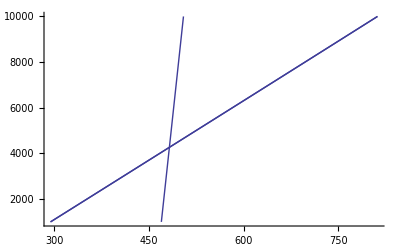

{{4267.2,482.303,{1,2}}}

```mathematica
Dataset[Dataset->HP32];  
CalcFormula["hs78b"];
phases={ann,phl,alm,py,gr,an,ky,qz};
rea=MakeRea[phases];
result=CalcRea[rea,CalcReaMin->1000,CalcReaMax->10000,Steps->10,CalcReaMode->PT,SampleFile->"hs78b",Screen->ScreenNo]
PlotRea[result]
CalcReaIntersection[result]
```